# Контролна работа №1 Група Г, задача 1 Фак. №2001261051

## Дадено е уравнението: x^2 - (b + 40) sinx/(x - 2) - 3(a + b + 1) = 0

```mathematica
f[x_]:=x^2-(1+40)Sin[x]/(x-2)-3(5+1+1)
```

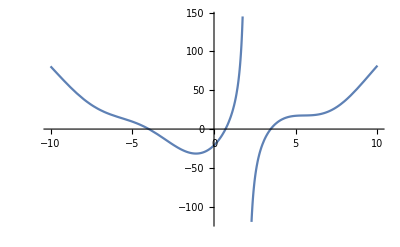

```mathematica
Plot[f[x],{x,-10,10}]
```

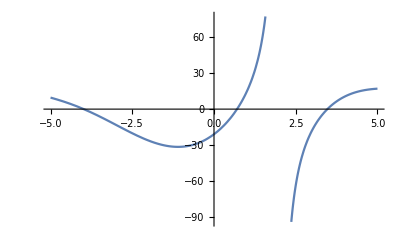

```mathematica
Plot[f[x],{x,-5,5}]
```

### 1. Да се намери броят на корените на уравнението и да се локализира най-големият от тях (в случай на повече от един).

Според графиката горе има 3 корена общо.

Локализиране на най-голям корен:

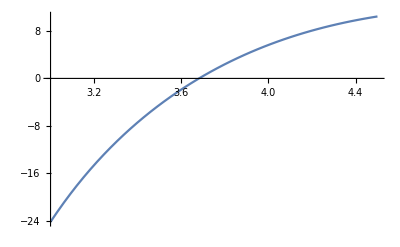

```mathematica
Plot[f[x],{x,3,4.5}]
```

```mathematica
f[3.]
```

-24.2093

```mathematica
f[4.]
```

5.64965

Извод:
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(3) = --24.2093 < 0 и f(4) = 5.64965 > 0
Функцията има различни знаци в двата края на разглеждания интервал [3; 4].
Следователно от (1) и (2) следва, че в интервала [3; 4] функцията има поне един
корен.

### 2. Да се направят 3 итерации по метода на разполовяването

```mathematica
f[x_]:=x^2-(1+40)Sin[x]/(x-2)-3(5+1+1)
For[
(*Начални условия - вземаме за 'а' и 'b' локализираните стойности от отгоре*)
n = 0; a=3.; b=4.,
n<=3,n++,
(*Тяло на цикъла*)
Print["|","n = ",n,"| a_n = ",a,"| b_n = ",b,"| m_n = ",m=(a+b)/2,"| f(m_n) = ",f[m],"| ε_n = ",(b-a)/2,"|"];
If[f[m]<0,a=m,b=m]
]
```

|n = 0| a_n = 3.| b_n = 4.| m_n = 3.5| f(m_n) = 0.838075| ε_n = 0.5|

|n = 1| a_n = 3.| b_n = 3.5| m_n = 3.25| f(m_n) = -6.8887| ε_n = 0.25|

|n = 2| a_n = 3.25| b_n = 3.5| m_n = 3.375| f(m_n) = -2.71261| ε_n = 0.125|

|n = 3| a_n = 3.375| b_n = 3.5| m_n = 3.4375| f(m_n) = -0.86643| ε_n = 0.0625|

### 3. Каква е грешката на полученото решение?

```mathematica
(*гледаме ϵ от последната итерация (в случая - 3тата)*)
```

Отг: грешката е 0.0625

### 4. Какъв е минималният брой итерации за достигане на точност 10^-10, ако се работи в избрания интервал?

```mathematica
f[x_]:=x^2-(1+40)Sin[x]/(x-2)-3(5+1+1)
For[
(*Начални условия - пробваме различни стойности за 'n', докато ϵ (грешката) не получи дадената точност от -10 като степен*)
n = 0; a=3.; b=4.,
n<=30,n++,
(*Тяло на цикъла*)
Print["|","n = ",n,"| a_n = ",a,"| b_n = ",b,"| m_n = ",m=(a+b)/2,"| f(m_n) = ",f[m],"| ε_n = ",(b-a)/2,"|"];
If[f[m]<0,a=m,b=m]
]
```

|n = 0| a_n = 3.| b_n = 4.| m_n = 3.5| f(m_n) = 0.838075| ε_n = 0.5|

|n = 1| a_n = 3.| b_n = 3.5| m_n = 3.25| f(m_n) = -6.8887| ε_n = 0.25|

|n = 2| a_n = 3.25| b_n = 3.5| m_n = 3.375| f(m_n) = -2.71261| ε_n = 0.125|

|n = 3| a_n = 3.375| b_n = 3.5| m_n = 3.4375| f(m_n) = -0.86643| ε_n = 0.0625|

|n = 4| a_n = 3.4375| b_n = 3.5| m_n = 3.46875| f(m_n) = 0.00274608| ε_n = 0.03125|

|n = 5| a_n = 3.4375| b_n = 3.46875| m_n = 3.45313| f(m_n) = -0.427518| ε_n = 0.015625|

|n = 6| a_n = 3.45313| b_n = 3.46875| m_n = 3.46094| f(m_n) = -0.211317| ε_n = 0.0078125|

|n = 7| a_n = 3.46094| b_n = 3.46875| m_n = 3.46484| f(m_n) = -0.10402| ε_n = 0.00390625|

|n = 8| a_n = 3.46484| b_n = 3.46875| m_n = 3.4668| f(m_n) = -0.0505704| ε_n = 0.00195313|

|n = 9| a_n = 3.4668| b_n = 3.46875| m_n = 3.46777| f(m_n) = -0.0238956| ε_n = 0.000976563|

|n = 10| a_n = 3.46777| b_n = 3.46875| m_n = 3.46826| f(m_n) = -0.0105706| ε_n = 0.000488281|

|n = 11| a_n = 3.46826| b_n = 3.46875| m_n = 3.46851| f(m_n) = -0.00391125| ε_n = 0.000244141|

|n = 12| a_n = 3.46851| b_n = 3.46875| m_n = 3.46863| f(m_n) = -0.00058233| ε_n = 0.00012207|

|n = 13| a_n = 3.46863| b_n = 3.46875| m_n = 3.46869| f(m_n) = 0.00108194| ε_n = 0.0000610352|

|n = 14| a_n = 3.46863| b_n = 3.46869| m_n = 3.46866| f(m_n) = 0.00024982| ε_n = 0.0000305176|

|n = 15| a_n = 3.46863| b_n = 3.46866| m_n = 3.46864| f(m_n) = -0.000166251| ε_n = 0.0000152588|

|n = 16| a_n = 3.46864| b_n = 3.46866| m_n = 3.46865| f(m_n) = 0.0000417858| ε_n = 7.62939×10^-6|

|n = 17| a_n = 3.46864| b_n = 3.46865| m_n = 3.46865| f(m_n) = -0.0000622322| ε_n = 3.8147×10^-6|

|n = 18| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = -0.0000102231| ε_n = 1.90735×10^-6|

|n = 19| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 0.0000157814| ε_n = 9.53674×10^-7|

|n = 20| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 2.77914×10^-6| ε_n = 4.76837×10^-7|

|n = 21| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = -3.72198×10^-6| ε_n = 2.38419×10^-7|

|n = 22| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = -4.71423×10^-7| ε_n = 1.19209×10^-7|

|n = 23| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 1.15386×10^-6| ε_n = 5.96046×10^-8|

|n = 24| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 3.41217×10^-7| ε_n = 2.98023×10^-8|

|n = 25| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = -6.51034×10^-8| ε_n = 1.49012×10^-8|

|n = 26| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 1.38057×10^-7| ε_n = 7.45058×10^-9|

|n = 27| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 3.64767×10^-8| ε_n = 3.72529×10^-9|

|n = 28| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = -1.43134×10^-8| ε_n = 1.86265×10^-9|

|n = 29| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = 1.10816×10^-8| ε_n = 9.31323×10^-10|

|n = 30| a_n = 3.46865| b_n = 3.46865| m_n = 3.46865| f(m_n) = -1.61585×10^-9| ε_n = 4.65661×10^-10|

Извод: минималният брой итерации за достигане на точност 10^-10 е 29.